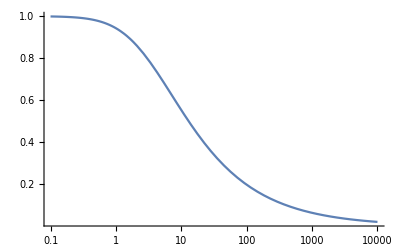

```mathematica
LogLinearPlot[Sqrt[1-1/((n+2)/n)^2],{n,0.1,10000},PlotRange->All]
```

```mathematica
Solve[g^-2+v^2==1&&g v==1]
```

{{g→-√2,v→-1/(√2)},{g→√2,v→1/(√2)}}

```mathematica
%//N
```

{{g→-1.41421,v→-0.707107},{g→1.41421,v→0.707107}}

```mathematica
Solve[ArcTan[v/Sqrt[1-v^2]]==Pi/6,v]//FullSimplify
```

{{v→1/2}}

```mathematica
Sin/@({1,2}Pi/6)
```

{1/2,(√3)/2}

```mathematica
1/Sqrt[1-#^2]&/@%
```

{2/(√3),2}

```mathematica
%//N
```

{1.1547,2.}

```mathematica
%22//N
```

{0.5,0.866025}

```mathematica
Sqrt[1-1/(20/18)^2]//N
```

0.43589

```mathematica
Solve[Sqrt[1-1/((n+2)/n)^2]==1/2,n]
```

{{n→2 (3-2 √3)},{n→2 (3+2 √3)}}

```mathematica
%//N
```

{{n→-0.928203},{n→12.9282}}

```mathematica
Sqrt[1-1/((n+2)/n)^2]/.n->10000.
```

0.019997